```mathematica
ClearAll[f]
in1 = 1;
in2 = 1;
f = {1};
For[i =1, Length[f] <1000,i= in1+in2,AppendTo[f,i]; in2=in1; in1= i; ]
```

```mathematica
For[i=0, i< Length[f]-1, i++, Print[N[f⟦i+1⟧/f⟦i⟧,100]]]
```

```mathematica
ClearAll[FirstDigit, Frequency]
FirstDigit[x_]:=First@First@RealDigits[x, 10,1];
Frequency = {0,0,0,0,0,0,0,0,0};
For[i=1, i<Length[f], i++, For[k=1, k<10, k++, If[FirstDigit[f⟦i⟧] == k,Frequency⟦k⟧= Frequency⟦k⟧+1]]]
Frequency
```

{301,177,125,95,80,67,56,53,45}

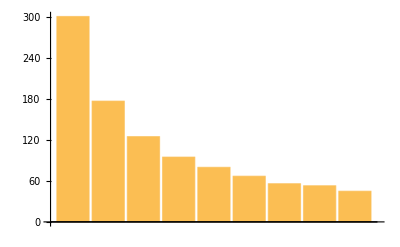

```mathematica
BarChart[Table[Frequency⟦i⟧, {i, 9}]]
```